```mathematica
L[x_,r_]=r x(1-x)
Logistic[x0_,n_,r_]:=NestList[L[#,r]&,x0,n]
DF[x_,r_]=D[L[x,r],x]
LYALogistic[list_,r_]:=1/Length[list]  Total[Log[Abs[DF[#,r]]]&/@list]
```

r (1-x) x

r (1-x)-r x

```mathematica
LYALogistic[Logistic[0.3,20,3.5],3.5]
DF[#,3.5]&/@Logistic[0.3,20,3.5]
```

-0.0380313

{1.4,-1.645,-1.27199,-1.81602,-0.976029,-2.14868,-0.316578,-2.57489,0.690027,-2.38693,0.223721,-2.59997,0.754934,-2.34004,0.112888,-2.61863,0.803607,-2.30211,0.0248509,-2.62469,0.819502}

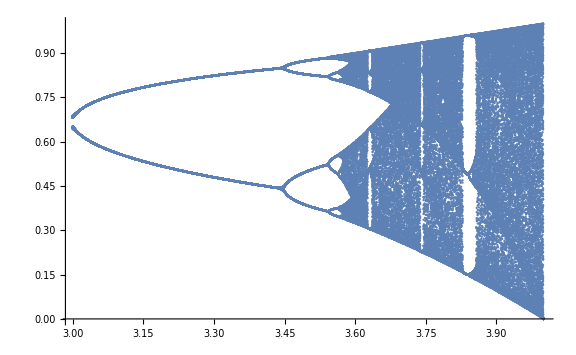

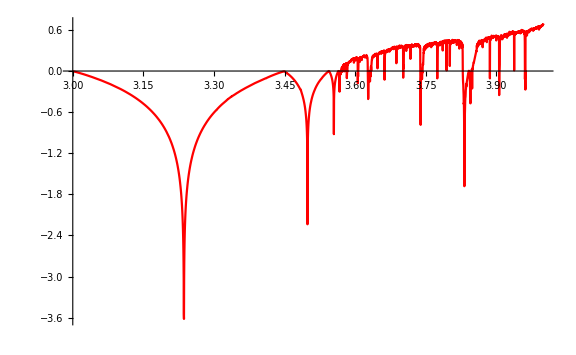

```mathematica
resolution=1000;
iterations=500;
rs=Range[3,4,(4-3)/resolution];
a=ListPlot[
Flatten[
Partition[
Riffle[
Logistic[0.5,iterations,#],
#][[200;;iterations]],
2]&/@rs
,1]
,ImageSize->Large]

b=Plot[LYALogistic[Logistic[0.3,1000,r],r],{r,3,4},ImageSize->Large,PlotStyle->Red,PlotRange->Full]
```